## Rössler eqs. for delayed-feedback control (Pyragas, etc.) Problem 11.24

```mathematica
Clear["Global`*"];
```

```mathematica
f[τ_]:=
(tend=300; a=0.2; b=0.2; c=5.7;k=0.2 UnitStep[t-100];
 eq={   x'[t]==-y[t]-z[t], 
        y'[t]==x[t]+a y[t]-k(y[t]-y[t-τ]),
        z'[t]==b+z[t](x[t]-c)                                       };
init={x[0]==5,y[0]==0,z[0]==0};
{xs,ys,zs}=NDSolveValue[{eq,init},{x,y,z},{t,0,tend}];
py=Plot[{ys[t]},{t,0,tend},PlotRange->{-12,12},ImageSize->{500,200}];
pyy=Plot[{k(ys[t]-ys[t-11.76])},{t,0,tend},PlotRange->{-2,2},ImageSize->{500,200}];
NIntegrate[(k(ys[t]-ys[t-τ]))^2,{t,tend-50,tend}])
```

```mathematica
f[11.76]
```

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

InterpolatingFunction::dmval: Input value {-11.7539} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.0197373

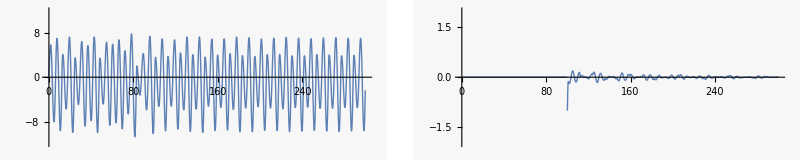

```mathematica
GraphicsRow[{py,pyy}]
```

```mathematica
f[5.88]
```

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

InterpolatingFunction::dmval: Input value {-11.7539} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.0000273776

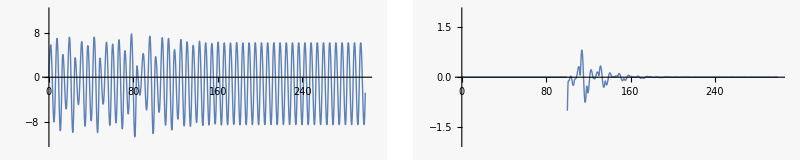

```mathematica
GraphicsRow[{py,pyy}]
```

```mathematica
f[9.3]
```

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

InterpolatingFunction::dmval: Input value {-11.7539} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.000416783

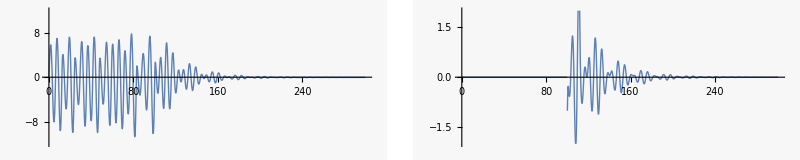

```mathematica
GraphicsRow[{py,pyy}]
```

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

InterpolatingFunction::dmval: Input value {-11.7539} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

InterpolatingFunction::dmval: Input value {-11.7539} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of NDSolveValue::ihist will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-11.7539} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

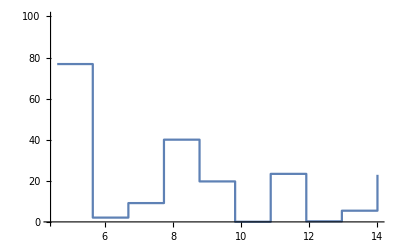

```mathematica
tdat=Table[f[τ],{τ,4.6,14,1}];   (* run with dτ=0.1, but takes a long time! *)
ListPlot[tdat,DataRange->{4.6,14},PlotRange->{0,100}]
```

Export data

```mathematica
dt=0.1;
yst=Table[ys[t],{t,0,tend,dt}];
(* 
SetDirectory[NotebookDirectory[]];
Export["pyragasdat1.dat",tdat,"Table"];
Export["pyragasdaty2.dat",yst,"Table"];
*)
```